```mathematica
A2Lattice = Flatten[Table[If[a+b+c==0&&1/2(a^2+b^2+c^2)≤8,{a,b,c},Nothing],{a,-8,8},{b,-8,8},{c,-8,8}],2];
A2Roots = Table[If[1/2a.a ==1,a,Nothing],{a,A2Lattice}];
l[ϵ1_,ϵ2_,σ1_,σ2_,σ3_,k1_,k2_,k3_,a1_,a2_,a3_]:=Product[Which[{k1,k2,k3}.{a1,a2,a3}<0&&i+j≤-{k1,k2,k3}.{a1,a2,a3}-1,(-ϵ1 i-ϵ2 j+{a1,a2,a3}.{σ1,σ2,σ3}),{k1,k2,k3}.{a1,a2,a3}>1&&i+j≤{k1,k2,k3}.{a1,a2,a3}-2,(ϵ1(i+1)+ϵ2(j+1)+{a1,a2,a3}.{σ1,σ2,σ3}),True,1],{i,0,2},{j,0,2}];
l[ϵ1_,ϵ2_,{σ1_,σ2_,σ3_},{k1_,k2_,k3_},{a1_,a2_,a3_}]:=l[ϵ1,ϵ2,σ1,σ2,σ3,k1,k2,k3,a1,a2,a3];
L[ϵ1_,ϵ2_,{σ1_,σ2_,σ3_},{k1_,k2_,k3_}]:=Product[l[ϵ1,ϵ2,{σ1,σ2,σ3},{k1,k2,k3},a],{a,A2Roots}]//Cancel;
lBig[ϵ1_,ϵ2_,σ1_,σ2_,σ3_,k1_,k2_,k3_,a1_,a2_,a3_]:=Product[Which[{k1,k2,k3}.{a1,a2,a3}<0&&i+j≤-{k1,k2,k3}.{a1,a2,a3}-1,({a1,a2,a3}.{σ1,σ2,σ3}),{k1,k2,k3}.{a1,a2,a3}>1&&i+j≤{k1,k2,k3}.{a1,a2,a3}-2,({a1,a2,a3}.{σ1,σ2,σ3}),True,1],{i,0,2},{j,0,2}];
lBig[ϵ1_,ϵ2_,{σ1_,σ2_,σ3_},{k1_,k2_,k3_},{a1_,a2_,a3_}]:=lBig[ϵ1,ϵ2,σ1,σ2,σ3,k1,k2,k3,a1,a2,a3];
LBig[ϵ1_,ϵ2_,{σ1_,σ2_,σ3_},{k1_,k2_,k3_}]:=Product[lBig[ϵ1,ϵ2,{σ1,σ2,σ3},{k1,k2,k3},a],{a,A2Roots}]//Cancel;
Subscript[Ž, 1][ϵ1_,ϵ2_,{σ1_,σ2_,σ3_}]:=1/(-ϵ1 ϵ2)Sum[(1/((+ϵ1+ϵ2+{σ1,σ2,σ3}.a)({σ1,σ2,σ3}.a)Product[If[ b.a==1, {σ1,σ2,σ3}.b,1],{b,A2Roots}]))//Cancel,{a,A2Roots}];
σ:={σ1,σ2,σ3};
```

```mathematica
Subscript[z, n_][ϵ1_,ϵ2_,{σ1_,σ2_,σ3_}]:=1/(n^2 ϵ1 ϵ2)Sum[If[1/2 k.k + m1+m2 == n,(((ϵ1 m1+(ϵ1+ϵ2) m2+k.{σ1,σ2,σ3}+k.k/2(2ϵ1+ϵ2))(ϵ1 m1+(ϵ1+ϵ2) m2+k.{σ1,σ2,σ3}+k.k/2(2ϵ1+ϵ2)-n(ϵ1+ϵ2)))/L[ϵ1,ϵ1+ϵ2,{σ1,σ2,σ3},k])If[m1==0,1,Subscript[z, m1][ϵ1,ϵ2,{σ1,σ2,σ3}+ϵ1 k]]If[m2==0,1,Subscript[z, m2][-ϵ2,ϵ1+ϵ2,{σ1,σ2,σ3}+ϵ1 k+ϵ2 k]]//Cancel,0],{k,A2Lattice},{m1,0,n-1},{m2,0,n-1}]
```

```mathematica
-Subscript[z, 1][1,-1,σ]//Simplify
```

(2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)

```mathematica
(((ϵ1 m1+(ϵ1+ϵ2) m2+k.{σ1,σ2,σ3}+k.k/2(2ϵ1+ϵ2))(ϵ1 m1+(ϵ1+ϵ2) m2+k.{σ1,σ2,σ3}+k.k/2(2ϵ1+ϵ2)-n(ϵ1+ϵ2)))/L[ϵ1,ϵ1+ϵ2,{σ1,σ2,σ3},k])/.{ϵ1->1,ϵ2->-1+ℏ}//Simplify
```

((m1+m2 ℏ+1/2 (1+ℏ) k.k+k.{σ1,σ2,σ3}) (m1-2 ℏ+m2 ℏ+1/2 (1+ℏ) k.k+k.{σ1,σ2,σ3}))/L[1,ℏ,{σ1,σ2,σ3},k]

```mathematica
Subscript[zExp, n_][ϵ1_,ϵ2_,{σ1_,σ2_,σ3_}]:=1/(n!)((2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))/(ϵ1 ϵ2(σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2))^n
```

```mathematica
Subscript[z, 1][ϵ,-ϵ,σ]//Simplify
```

-(2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))/(ϵ^2 (σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)

```mathematica
((Subscript[z, 2][1,-1+ℏ,σ/γ])/(Subscript[zExp, 2][1,-1,σ/γ])//Factor)/.ℏ->0
```

((σ1-σ2)^3 (σ1-σ3)^3 (σ2-σ3)^3 (-3 γ^8 σ1^2+5 γ^6 σ1^4-γ^4 σ1^6-γ^2 σ1^8+3 γ^8 σ1 σ2-10 γ^6 σ1^3 σ2+3 γ^4 σ1^5 σ2+4 γ^2 σ1^7 σ2-3 γ^8 σ2^2+15 γ^6 σ1^2 σ2^2-33 γ^4 σ1^4 σ2^2+11 γ^2 σ1^6 σ2^2-2 σ1^8 σ2^2-10 γ^6 σ1 σ2^3+61 γ^4 σ1^3 σ2^3-47 γ^2 σ1^5 σ2^3+8 σ1^7 σ2^3+5 γ^6 σ2^4-33 γ^4 σ1^2 σ2^4+65 γ^2 σ1^4 σ2^4-16 σ1^6 σ2^4+3 γ^4 σ1 σ2^5-47 γ^2 σ1^3 σ2^5+20 σ1^5 σ2^5-γ^4 σ2^6+11 γ^2 σ1^2 σ2^6-16 σ1^4 σ2^6+4 γ^2 σ1 σ2^7+8 σ1^3 σ2^7-γ^2 σ2^8-2 σ1^2 σ2^8+3 γ^8 σ1 σ3-10 γ^6 σ1^3 σ3+3 γ^4 σ1^5 σ3+4 γ^2 σ1^7 σ3+3 γ^8 σ2 σ3+51 γ^4 σ1^4 σ2 σ3-50 γ^2 σ1^6 σ2 σ3+4 σ1^8 σ2 σ3-51 γ^4 σ1^3 σ2^2 σ3+75 γ^2 σ1^5 σ2^2 σ3-8 σ1^7 σ2^2 σ3-10 γ^6 σ2^3 σ3-51 γ^4 σ1^2 σ2^3 σ3-25 γ^2 σ1^4 σ2^3 σ3+8 σ1^6 σ2^3 σ3+51 γ^4 σ1 σ2^4 σ3-25 γ^2 σ1^3 σ2^4 σ3-4 σ1^5 σ2^4 σ3+3 γ^4 σ2^5 σ3+75 γ^2 σ1^2 σ2^5 σ3-4 σ1^4 σ2^5 σ3-50 γ^2 σ1 σ2^6 σ3+8 σ1^3 σ2^6 σ3+4 γ^2 σ2^7 σ3-8 σ1^2 σ2^7 σ3+4 σ1 σ2^8 σ3-3 γ^8 σ3^2+15 γ^6 σ1^2 σ3^2-33 γ^4 σ1^4 σ3^2+11 γ^2 σ1^6 σ3^2-2 σ1^8 σ3^2-51 γ^4 σ1^3 σ2 σ3^2+75 γ^2 σ1^5 σ2 σ3^2-8 σ1^7 σ2 σ3^2+15 γ^6 σ2^2 σ3^2+153 γ^4 σ1^2 σ2^2 σ3^2-150 γ^2 σ1^4 σ2^2 σ3^2+16 σ1^6 σ2^2 σ3^2-51 γ^4 σ1 σ2^3 σ3^2+100 γ^2 σ1^3 σ2^3 σ3^2-16 σ1^5 σ2^3 σ3^2-33 γ^4 σ2^4 σ3^2-150 γ^2 σ1^2 σ2^4 σ3^2+20 σ1^4 σ2^4 σ3^2+75 γ^2 σ1 σ2^5 σ3^2-16 σ1^3 σ2^5 σ3^2+11 γ^2 σ2^6 σ3^2+16 σ1^2 σ2^6 σ3^2-8 σ1 σ2^7 σ3^2-2 σ2^8 σ3^2-10 γ^6 σ1 σ3^3+61 γ^4 σ1^3 σ3^3-47 γ^2 σ1^5 σ3^3+8 σ1^7 σ3^3-10 γ^6 σ2 σ3^3-51 γ^4 σ1^2 σ2 σ3^3-25 γ^2 σ1^4 σ2 σ3^3+8 σ1^6 σ2 σ3^3-51 γ^4 σ1 σ2^2 σ3^3+100 γ^2 σ1^3 σ2^2 σ3^3-16 σ1^5 σ2^2 σ3^3+61 γ^4 σ2^3 σ3^3+100 γ^2 σ1^2 σ2^3 σ3^3-25 γ^2 σ1 σ2^4 σ3^3-47 γ^2 σ2^5 σ3^3-16 σ1^2 σ2^5 σ3^3+8 σ1 σ2^6 σ3^3+8 σ2^7 σ3^3+5 γ^6 σ3^4-33 γ^4 σ1^2 σ3^4+65 γ^2 σ1^4 σ3^4-16 σ1^6 σ3^4+51 γ^4 σ1 σ2 σ3^4-25 γ^2 σ1^3 σ2 σ3^4-4 σ1^5 σ2 σ3^4-33 γ^4 σ2^2 σ3^4-150 γ^2 σ1^2 σ2^2 σ3^4+20 σ1^4 σ2^2 σ3^4-25 γ^2 σ1 σ2^3 σ3^4+65 γ^2 σ2^4 σ3^4+20 σ1^2 σ2^4 σ3^4-4 σ1 σ2^5 σ3^4-16 σ2^6 σ3^4+3 γ^4 σ1 σ3^5-47 γ^2 σ1^3 σ3^5+20 σ1^5 σ3^5+3 γ^4 σ2 σ3^5+75 γ^2 σ1^2 σ2 σ3^5-4 σ1^4 σ2 σ3^5+75 γ^2 σ1 σ2^2 σ3^5-16 σ1^3 σ2^2 σ3^5-47 γ^2 σ2^3 σ3^5-16 σ1^2 σ2^3 σ3^5-4 σ1 σ2^4 σ3^5+20 σ2^5 σ3^5-γ^4 σ3^6+11 γ^2 σ1^2 σ3^6-16 σ1^4 σ3^6-50 γ^2 σ1 σ2 σ3^6+8 σ1^3 σ2 σ3^6+11 γ^2 σ2^2 σ3^6+16 σ1^2 σ2^2 σ3^6+8 σ1 σ2^3 σ3^6-16 σ2^4 σ3^6+4 γ^2 σ1 σ3^7+8 σ1^3 σ3^7+4 γ^2 σ2 σ3^7-8 σ1^2 σ2 σ3^7-8 σ1 σ2^2 σ3^7+8 σ2^3 σ3^7-γ^2 σ3^8-2 σ1^2 σ3^8+4 σ1 σ2 σ3^8-2 σ2^2 σ3^8))/(2 (-γ+σ1-σ2) (γ+σ1-σ2) (-σ1+σ2) (-γ-σ1+σ2) (γ-σ1+σ2) (-γ+σ1-σ3) (γ+σ1-σ3) (-γ+σ2-σ3) (γ+σ2-σ3) (-σ1+σ3) (-γ-σ1+σ3) (γ-σ1+σ3) (-σ2+σ3) (-γ-σ2+σ3) (γ-σ2+σ3) (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)^2)

```mathematica
Out[266]/.γ->0//Simplify
```

1

```mathematica
((ϵ1 m1+(ϵ1+ϵ2) m2)(ϵ1 m1-(ϵ1+ϵ2) m1))//FullSimplify
```

-m1 ϵ2 (m1 ϵ1+m2 (ϵ1+ϵ2))

```mathematica
LBig[ϵ1,ϵ1+ϵ2,{σ1,σ2,σ3},{0,0,0}]
```

1

```mathematica
n=5;

1/(n^2 ϵ1 ϵ2  Subscript[zExp, n][ϵ1,ϵ2,{σ1,σ2,σ3}])Join[Table[If[1/2 k.k + m1+m2 == n,(-m1 ϵ2 (m1 ϵ1+m2 (ϵ1+ϵ2))/1) If[m1==0,1,Subscript[zExp, m1][ϵ1,ϵ2,{σ1,σ2,σ3}]]If[m2==0,1,Subscript[zExp, m2][-ϵ2,ϵ1+ϵ2,{σ1,σ2,σ3}]]//Cancel,Nothing],{k,{{0,0,0}}},{m1,0,n-1},{m2,0,n-1}]//Flatten//Simplify,
Table[If[1/2 k.k + m1+m2 == n&&k.k≠0,(k.{σ1,σ2,σ3}) (k.{σ1,σ2,σ3})/LBig[ϵ1,ϵ1+ϵ2,{σ1,σ2,σ3},k]If[m1==0,1,Subscript[zExp, m1][ϵ1,ϵ2,{σ1,σ2,σ3}]]If[m2==0,1,Subscript[zExp, m2][-ϵ2,ϵ1+ϵ2,{σ1,σ2,σ3}]]//Cancel,Nothing],{k,A2Lattice},{m1,0,n-1},{m2,0,n-1}]//Flatten//Simplify
]
```

{-(ϵ1^3 (5 ϵ1+4 ϵ2))/(5 (ϵ1+ϵ2)^4),(4 ϵ1^2 (5 ϵ1+3 ϵ2))/(5 (ϵ1+ϵ2)^3),-(6 ϵ1 (5 ϵ1+2 ϵ2))/(5 (ϵ1+ϵ2)^2),(4 (5 ϵ1+ϵ2))/(5 (ϵ1+ϵ2)),-(6 ϵ1^4 ϵ2^3 (σ1-σ2)^4 (σ2-σ3)^4)/(5 (ϵ1+ϵ2) (σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(6 ϵ1^3 ϵ2^3 (σ1-σ2)^4 (σ2-σ3)^4)/(5 (σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(3 ϵ1^4 ϵ2^2 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2)/(10 (ϵ1+ϵ2)^2 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-(3 ϵ1^3 ϵ2^2 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2)/(5 (ϵ1+ϵ2) (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 ϵ1^2 ϵ2^2 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2)/(10 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-(6 ϵ1^4 ϵ2^3 (σ1-σ3)^4 (σ2-σ3)^4)/(5 (ϵ1+ϵ2) (σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(6 ϵ1^3 ϵ2^3 (σ1-σ3)^4 (σ2-σ3)^4)/(5 (σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(3 ϵ1^4 ϵ2^2 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2)/(10 (ϵ1+ϵ2)^2 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-(3 ϵ1^3 ϵ2^2 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2)/(5 (ϵ1+ϵ2) (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 ϵ1^2 ϵ2^2 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2)/(10 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-(ϵ1^4 (σ1-σ2) (σ2-σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(2 ϵ1^3 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(3 ϵ1^2 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(2 ϵ1 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-((σ1-σ2) (σ2-σ3))/(10 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(ϵ1^4 (σ1-σ3) (σ2-σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(2 ϵ1^3 (σ1-σ3) (σ2-σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(3 ϵ1^2 (σ1-σ3) (σ2-σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(2 ϵ1 (σ1-σ3) (σ2-σ3))/(5 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ3) (σ2-σ3))/(10 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(3 ϵ1^4 ϵ2^2 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2)/(10 (ϵ1+ϵ2)^2 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 ϵ1^3 ϵ2^2 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2)/(5 (ϵ1+ϵ2) (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-(3 ϵ1^2 ϵ2^2 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2)/(10 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-(6 ϵ1^4 ϵ2^3 (σ1-σ2)^4 (σ1-σ3)^4)/(5 (ϵ1+ϵ2) (σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(6 ϵ1^3 ϵ2^3 (σ1-σ2)^4 (σ1-σ3)^4)/(5 (σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(ϵ1^4 (σ1-σ2) (σ1-σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(2 ϵ1^3 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(3 ϵ1^2 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(2 ϵ1 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ2) (σ1-σ3))/(10 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(ϵ1^4 (σ1-σ2) (σ1-σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(2 ϵ1^3 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(3 ϵ1^2 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(2 ϵ1 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ2) (σ1-σ3))/(10 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(6 ϵ1^4 ϵ2^3 (σ1-σ2)^4 (σ1-σ3)^4)/(5 (ϵ1+ϵ2) (σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(6 ϵ1^3 ϵ2^3 (σ1-σ2)^4 (σ1-σ3)^4)/(5 (σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-(3 ϵ1^4 ϵ2^2 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2)/(10 (ϵ1+ϵ2)^2 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 ϵ1^3 ϵ2^2 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2)/(5 (ϵ1+ϵ2) (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-(3 ϵ1^2 ϵ2^2 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2)/(10 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(ϵ1^4 (σ1-σ3) (σ2-σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(2 ϵ1^3 (σ1-σ3) (σ2-σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(3 ϵ1^2 (σ1-σ3) (σ2-σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(2 ϵ1 (σ1-σ3) (σ2-σ3))/(5 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ3) (σ2-σ3))/(10 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(ϵ1^4 (σ1-σ2) (σ2-σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(2 ϵ1^3 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(3 ϵ1^2 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(2 ϵ1 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-((σ1-σ2) (σ2-σ3))/(10 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(3 ϵ1^4 ϵ2^2 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2)/(10 (ϵ1+ϵ2)^2 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-(3 ϵ1^3 ϵ2^2 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2)/(5 (ϵ1+ϵ2) (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 ϵ1^2 ϵ2^2 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2)/(10 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-(6 ϵ1^4 ϵ2^3 (σ1-σ3)^4 (σ2-σ3)^4)/(5 (ϵ1+ϵ2) (σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(6 ϵ1^3 ϵ2^3 (σ1-σ3)^4 (σ2-σ3)^4)/(5 (σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(3 ϵ1^4 ϵ2^2 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2)/(10 (ϵ1+ϵ2)^2 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-(3 ϵ1^3 ϵ2^2 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2)/(5 (ϵ1+ϵ2) (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 ϵ1^2 ϵ2^2 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2)/(10 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-(6 ϵ1^4 ϵ2^3 (σ1-σ2)^4 (σ2-σ3)^4)/(5 (ϵ1+ϵ2) (σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(6 ϵ1^3 ϵ2^3 (σ1-σ2)^4 (σ2-σ3)^4)/(5 (σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4)}

```mathematica
(Out[142]/.{σ1->σ1/ϵ,σ2->σ2/ϵ,σ3->σ3/ϵ}//Factor)/.{ϵ->0}//Total//Simplify
```

1

```mathematica
Table[If[ m1+m2 == n,1/(n^2 ϵ1 ϵ2)(-m1 ϵ2 (m1 ϵ1+m2 (ϵ1+ϵ2))/1) ((m1+m2)!)/(m1!m2!)(ϵ1^n ϵ2^n)/(ϵ1^m1 ϵ2^m1(-ϵ2)^m2(ϵ1+ϵ2)^m2)//Cancel,Nothing],{m1,0,n-1},{m2,0,n-1}]//Simplify
```

{{},{(ϵ1^4 (6 ϵ1+5 ϵ2))/(6 (ϵ1+ϵ2)^5)},{-(5 ϵ1^3 (3 ϵ1+2 ϵ2))/(3 (ϵ1+ϵ2)^4)},{(5 ϵ1^2 (2 ϵ1+ϵ2))/(ϵ1+ϵ2)^3},{-(10 ϵ1 (3 ϵ1+ϵ2))/(3 (ϵ1+ϵ2)^2)},{(5 (6 ϵ1+ϵ2))/(6 (ϵ1+ϵ2))}}

```mathematica
n=3;
ϵ2^(n-1)/(n (ϵ1+ϵ2)^(n-1))+Sum[If[ m1+m2 == n,1/(n^2 ϵ1 ϵ2)(-m1 ϵ2 (m1 ϵ1+m2 (ϵ1+ϵ2))/1) ((m1+m2)!)/(m1!m2!)(ϵ1^n ϵ2^n)/(ϵ1^m1 ϵ2^m1(-ϵ2)^m2(ϵ1+ϵ2)^m2)//Cancel,0],{m1,0,n-1},{m2,0,n-1}]//FullSimplify
```

1

```mathematica
n=10;
(n^2 ϵ1 ϵ2 ϵ2^(n-1))/(n (ϵ1+ϵ2)^(n-1))+Sum[If[ m1+m2 == n,(-m1 ϵ2 (m1 ϵ1+m2 (ϵ1+ϵ2))/1) ((m1+m2)!)/(m1!m2!)(ϵ1^n ϵ2^n)/(ϵ1^m1 ϵ2^m1(-ϵ2)^m2(ϵ1+ϵ2)^m2)//Cancel,0],{m1,0,n-1},{m2,0,n-1}]//FullSimplify
```

100 ϵ1 ϵ2

```mathematica
1/(n^2 ϵ1 ϵ2)Sum[If[ m1+m2 == n,(-m1 ϵ2 (m1 ϵ1+m2 (ϵ1+ϵ2))/1) ((m1+m2)!)/(m1!m2!)(-(ϵ1+ϵ2)/ϵ1)^-m2//Cancel,0],{m1,0,n},{m2,0,n}]//FullSimplify
```

-ϵ2^9/(10 (ϵ1+ϵ2)^9)

```mathematica
1/(n^2 ϵ1 ϵ2)Sum[If[ m1+m2 == n,(-m1 ϵ2 (+m2 (ϵ1+ϵ2))/1) ((m1+m2)!)/(m1!m2!)(-(ϵ1+ϵ2)/ϵ1)^-m2//Cancel,0],{m1,0,n-1},{m2,0,n-1}]//FullSimplify
1/(n^2 ϵ1 ϵ2)Sum[(-(n-m2)^2 ϵ1 ϵ2 ) ((n)!)/((n-m2)!m2!)(-(ϵ1+ϵ2)/ϵ1)^-m2//Cancel,{m2,1,n-1}]//FullSimplify
1/(n^2 ϵ1 ϵ2)Sum[(-(n-m2)^2 ϵ1 ϵ2 ) ((n)!)/((n-m2)!m2!)(-(ϵ1+ϵ2)/ϵ1)^-m2//Cancel,{m2,0,0}]//FullSimplify
```

(9 ϵ2^8)/(10 (ϵ1+ϵ2)^8)

(ϵ1 (10 ϵ1^8+90 ϵ1^7 ϵ2+360 ϵ1^6 ϵ2^2+840 ϵ1^5 ϵ2^3+1260 ϵ1^4 ϵ2^4+1260 ϵ1^3 ϵ2^5+840 ϵ1^2 ϵ2^6+360 ϵ1 ϵ2^7+81 ϵ2^8))/(10 (ϵ1+ϵ2)^9)

-1

```mathematica
(ϵ1 (10 ϵ1^8+90 ϵ1^7 ϵ2+360 ϵ1^6 ϵ2^2+840 ϵ1^5 ϵ2^3+1260 ϵ1^4 ϵ2^4+1260 ϵ1^3 ϵ2^5+840 ϵ1^2 ϵ2^6+360 ϵ1 ϵ2^7+81 ϵ2^8))/(10 (ϵ1+ϵ2)^9)-(-(ϵ2^8 (9 ϵ1+10 ϵ2))/(10 (ϵ1+ϵ2)^9)+1)//Simplify
```

0

```mathematica
n=10;ϵ2^(n-1)/(n (ϵ1+ϵ2)^(n-1))+1/(n^2 ϵ1 ϵ2)Sum[If[ m1+m2 == n,(-m1 ϵ2 (m1 ϵ1+m2 (ϵ1+ϵ2))/1) ((m1+m2)!)/(m1!m2!)(-(ϵ1+ϵ2)/ϵ1)^-m2//Cancel,0],{m1,0,n-1},{m2,0,n-1}]//FullSimplify
1/(n^2 ϵ1 ϵ2)Sum[(-(n-m2)m2 ϵ2 (ϵ1+ϵ2) ) ((n)!)/((n-m2)!m2!)(-(ϵ1+ϵ2)/ϵ1)^-m2//Cancel,{m2,1,n-1}]//FullSimplify
1/(n^2 ϵ1 ϵ2)Sum[If[ m1+m2 == n,(-m1 ϵ2 (+m2 (ϵ1+ϵ2))/1) ((m1+m2)!)/(m1!m2!)(-(ϵ1+ϵ2)/ϵ1)^-m2//Cancel,0],{m1,0,n-1},{m2,0,n-1}]//FullSimplify
1/(n^2 ϵ1 ϵ2)Sum[(-(n-m2)^2 ϵ1 ϵ2 ) ((n)!)/((n-m2)!m2!)(-(ϵ1+ϵ2)/ϵ1)^-m2//Cancel,{m2,1,n-1}]//FullSimplify
1/(n^2 ϵ1 ϵ2)Sum[If[ m1+m2 == n,(-m1 ϵ2 (m1 ϵ1)/1) ((m1+m2)!)/(m1!m2!)(-(ϵ1+ϵ2)/ϵ1)^-m2//Cancel,0],{m1,0,n-1},{m2,0,n-1}]//FullSimplify
```

1

(9 ϵ2^8)/(10 (ϵ1+ϵ2)^8)

(9 ϵ2^8)/(10 (ϵ1+ϵ2)^8)

(ϵ1 (10 ϵ1^8+90 ϵ1^7 ϵ2+360 ϵ1^6 ϵ2^2+840 ϵ1^5 ϵ2^3+1260 ϵ1^4 ϵ2^4+1260 ϵ1^3 ϵ2^5+840 ϵ1^2 ϵ2^6+360 ϵ1 ϵ2^7+81 ϵ2^8))/(10 (ϵ1+ϵ2)^9)

(ϵ1 (10 ϵ1^8+90 ϵ1^7 ϵ2+360 ϵ1^6 ϵ2^2+840 ϵ1^5 ϵ2^3+1260 ϵ1^4 ϵ2^4+1260 ϵ1^3 ϵ2^5+840 ϵ1^2 ϵ2^6+360 ϵ1 ϵ2^7+81 ϵ2^8))/(10 (ϵ1+ϵ2)^9)

```mathematica
ϵ2^(n-1)/(n (ϵ1+ϵ2)^(n-1))+(9 ϵ2^8)/(10 (ϵ1+ϵ2)^8)+(ϵ1 (10 ϵ1^8+90 ϵ1^7 ϵ2+360 ϵ1^6 ϵ2^2+840 ϵ1^5 ϵ2^3+1260 ϵ1^4 ϵ2^4+1260 ϵ1^3 ϵ2^5+840 ϵ1^2 ϵ2^6+360 ϵ1 ϵ2^7+81 ϵ2^8))/(10 (ϵ1+ϵ2)^9)//Simplify
```

1

```mathematica
E6RootLattice = Flatten[Table[If[EvenQ[a+b+c+d+e+3f]&&IntegerQ[a-b]&&IntegerQ[a-c]&&IntegerQ[a-d]&&IntegerQ[a-e]&&IntegerQ[a-f]&&IntegerQ[b-c]&&IntegerQ[b-d]&&IntegerQ[b-e]&&IntegerQ[b-f]&&IntegerQ[c-d]&&IntegerQ[c-e]&&IntegerQ[c-f]&&IntegerQ[d-e]&&IntegerQ[d-f],{a,b,c,d,e,f,f,f},Nothing],{a,-2,2,1/2},{b,-2,2,1/2},{c,-2,2,1/2},{d,-2,2,1/2},{e,-2,2,1/2},{f,-2,2,1/2}],5];
E6Roots = Join[Flatten[Table[If[(a b c d e f^3==1),1/2{a,b,c,d,e,f,f,f},Nothing],{a,-1,1,2},{b,-1,1,2},{c,-1,1,2},{d,-1,1,2},{e,-1,1,2},{f,-1,1,2}],5],Flatten[Table[If[(a^2+b^2+c^2+d^2+e^2==2),{a,b,c,d,e,0,0,0},Nothing],{a,-1,1},{b,-1,1},{c,-1,1},{d,-1,1},{e,-1,1}],4]];
```

```mathematica
2(12-2)+2 2
```

24

```mathematica
2(12-4)
```

16

```mathematica
Table[Table[If[a.b==1,1,Nothing],{b,E6Roots}]//Length,{a,Table[If[1/2 c.c ==2,c,Nothing],{c,E6RootLattice}]}]//Tally
```

{{16,270}}

```mathematica
16+8
```

24

```mathematica
E6Roots//Length
```

72

```mathematica
Table[If[1/2 c.c ==2,c,Nothing],{c,E6RootLattice}]//Length
```

270

```mathematica
Table[Table[If[a.b==-1,1,Nothing],{b,A2Lattice}]//Length,{a,A2Lattice}]//Tally
```

{{1,12},{0,13},{4,6}}

```mathematica
Table[(ϵ^(2 3)L[ea,eb,σ/ϵ,a]//Factor)/.ϵ->0,{a,A2Lattice}]
Table[(ϵ^(2 3)L[ea,eb,σ/ϵ,a]//Factor)/.ϵ->0,{a,A2Roots}]
Table[(LBig[1,-1,σ,a]//Factor),{a,A2Roots}]
```

Power::infy: Infinite expression 1/0^16 encountered.

Power::infy: Infinite expression 1/0^12 encountered.

Power::infy: Infinite expression 1/0^16 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity,-(σ1-σ2) (σ1-σ3)^4 (σ2-σ3),(σ1-σ2)^4 (σ1-σ3) (σ2-σ3),ComplexInfinity,ComplexInfinity,(σ1-σ2) (σ1-σ3) (σ2-σ3)^4,0,(σ1-σ2) (σ1-σ3) (σ2-σ3)^4,ComplexInfinity,ComplexInfinity,(σ1-σ2)^4 (σ1-σ3) (σ2-σ3),-(σ1-σ2) (σ1-σ3)^4 (σ2-σ3),ComplexInfinity,ComplexInfinity,ComplexInfinity,ComplexInfinity}

{-(σ1-σ2) (σ1-σ3)^4 (σ2-σ3),(σ1-σ2)^4 (σ1-σ3) (σ2-σ3),(σ1-σ2) (σ1-σ3) (σ2-σ3)^4,(σ1-σ2) (σ1-σ3) (σ2-σ3)^4,(σ1-σ2)^4 (σ1-σ3) (σ2-σ3),-(σ1-σ2) (σ1-σ3)^4 (σ2-σ3)}

{-(σ1-σ2) (σ1-σ3)^4 (σ2-σ3),(σ1-σ2)^4 (σ1-σ3) (σ2-σ3),(σ1-σ2) (σ1-σ3) (σ2-σ3)^4,(σ1-σ2) (σ1-σ3) (σ2-σ3)^4,(σ1-σ2)^4 (σ1-σ3) (σ2-σ3),-(σ1-σ2) (σ1-σ3)^4 (σ2-σ3)}

```mathematica
Table[(σ.a)^4 Product[If[(2 b.a)/(a.a)==1,σ.b,1],{b,A2Roots}],{a,A2Roots}]
```

{(-σ1+σ2) (-σ1+σ3)^4 (-σ2+σ3),(-σ1+σ2)^4 (σ2-σ3) (-σ1+σ3),(σ1-σ2) (-σ1+σ3) (-σ2+σ3)^4,(-σ1+σ2) (σ1-σ3) (σ2-σ3)^4,(σ1-σ2)^4 (σ1-σ3) (-σ2+σ3),(σ1-σ2) (σ1-σ3)^4 (σ2-σ3)}

```mathematica
Table[Product[(σ.a)^4 Product[If[(2 b.a)/(a.a)==1,σ.b,1],{b,A2Roots}],{a,A2Roots}],{a,A2Roots}]
```

{(σ1-σ2)^6 (-σ1+σ2)^6 (σ1-σ3)^6 (σ2-σ3)^6 (-σ1+σ3)^6 (-σ2+σ3)^6,(σ1-σ2)^6 (-σ1+σ2)^6 (σ1-σ3)^6 (σ2-σ3)^6 (-σ1+σ3)^6 (-σ2+σ3)^6,(σ1-σ2)^6 (-σ1+σ2)^6 (σ1-σ3)^6 (σ2-σ3)^6 (-σ1+σ3)^6 (-σ2+σ3)^6,(σ1-σ2)^6 (-σ1+σ2)^6 (σ1-σ3)^6 (σ2-σ3)^6 (-σ1+σ3)^6 (-σ2+σ3)^6,(σ1-σ2)^6 (-σ1+σ2)^6 (σ1-σ3)^6 (σ2-σ3)^6 (-σ1+σ3)^6 (-σ2+σ3)^6,(σ1-σ2)^6 (-σ1+σ2)^6 (σ1-σ3)^6 (σ2-σ3)^6 (-σ1+σ3)^6 (-σ2+σ3)^6}

```mathematica
Table[(LBig[1,-1,σ,a]//Factor)/(-(σ.a)^4 Product[If[(2 b.a)/(a.a)==1,σ.b,1],{b,A2Roots}])//Cancel,{a,A2Roots}]
A2len3= Table[If[1/2a.a ==3,a,Nothing],{a,A2Lattice}];
Table[(LBig[1,-1,σ,a]//Factor)/Product[If[(2 b.a)/(a.a)==1,σ.b,1],{b,A2Roots}]^9//Cancel,{a,A2len3}]
A2len4= Table[If[1/2a.a ==4,a,Nothing],{a,A2Lattice}];
Table[(LBig[1,-1,σ,a]//Factor)/(Product[If[(2 b.a)/(a.a)==1,σ.b,1],{b,A2Roots}]^4 Product[If[(2 b.a)/(a.a)==1,σ.b,1],{b,A2Roots}]^14)//Cancel,{a,A2len4}]
```

{1,1,1,1,1,1}

{1,1,1,1,1,1}

{((σ1-σ2)^4 (σ2-σ3)^4)/(σ1-σ3)^4,((σ1-σ3)^4 (σ2-σ3)^4)/(σ1-σ2)^4,((σ1-σ2)^4 (σ1-σ3)^4)/(σ2-σ3)^4,((σ1-σ2)^4 (σ1-σ3)^4)/(σ2-σ3)^4,((σ1-σ3)^4 (σ2-σ3)^4)/(σ1-σ2)^4,((σ1-σ2)^4 (σ2-σ3)^4)/(σ1-σ3)^4}

```mathematica
A2len4
```

{{-2,0,2},{-2,2,0},{0,-2,2},{0,2,-2},{2,-2,0},{2,0,-2}}

```mathematica
Table[If[1/2a.a ==2,a,Nothing],{a,A2Lattice}]
```

{}

```mathematica
Flatten[Table[If[a+b==0&&1/2(a^2+b^2)==4,{a,b},Nothing],{a,-3,3},{b,-3,3}],1]
```

{{-2,2},{2,-2}}

```mathematica
Flatten[Table[If[a+b+c==0&&1/2(a^2+b^2+c^2)==3,{a,b,c},Nothing],{a,-3,3},{b,-3,3},{c,-3,3}],2]
```

{{-2,1,1},{-1,-1,2},{-1,2,-1},{1,-2,1},{1,1,-2},{2,-1,-1}}

```mathematica
Table[1/((σ.a)^2 Product[If[(2 b.a)/(a.a)==1,σ.b,1],{b,A2Roots}]),{a,A2Roots}]
```

{1/((-σ1+σ2) (-σ1+σ3)^2 (-σ2+σ3)),1/((-σ1+σ2)^2 (σ2-σ3) (-σ1+σ3)),1/((σ1-σ2) (-σ1+σ3) (-σ2+σ3)^2),1/((-σ1+σ2) (σ1-σ3) (σ2-σ3)^2),1/((σ1-σ2)^2 (σ1-σ3) (-σ2+σ3)),1/((σ1-σ2) (σ1-σ3)^2 (σ2-σ3))}

```mathematica
(-m1 ϵ2 (m1 ϵ1)/1) ((m1+m2)!)/(m1!m2!)(-(ϵ1+ϵ2)/ϵ1)^-m2/.{m1->x-m2}
```

-((-m2+x)^2 ϵ1 ϵ2 (-(ϵ1+ϵ2)/ϵ1)^-m2 x!)/(m2! (-m2+x)!)

```mathematica
1+(9 ϵ2^8)/(10 (ϵ1+ϵ2)^8)-(ϵ2^8 (9 ϵ1+10 ϵ2))/(10 (ϵ1+ϵ2)^9)//FullSimplify
```

1-ϵ2^9/(10 (ϵ1+ϵ2)^9)

```mathematica
1+((x-1) ϵ2^(x-2))/(x (ϵ1+ϵ2)^(x-2))-(ϵ2^(x-2) ((x-1) ϵ1+x ϵ2))/(x (ϵ1+ϵ2)^(x-1))//FullSimplify
```

1-(ϵ2^(-1+x) (ϵ1+ϵ2)^(1-x))/x

```mathematica
Sum[(-(n-m2) ϵ1 ϵ2 ) ((n)!)/((n-m2)!m2!)(-1/x)^-m2//Cancel,{m2,0,n-1}]//Simplify
```

-5 (-1+x)^4 ϵ1 ϵ2

```mathematica
Simplify[(ϵ1^(m1+m2)ϵ2^(m1+m2))/(ϵ1^m1 ϵ2^m1(-ϵ2)^m2(ϵ1+ϵ2)^m2),{ϵ1>0,ϵ2>0}]
```

(-(ϵ1+ϵ2)/ϵ1)^-m2

```mathematica
n=4;
Sum[If[ m1+m2 == n,1/(n^2 ϵ1 ϵ2)(-m1 ϵ2 (m1 ϵ1+m2 (ϵ1+ϵ2))/1) ((m1+m2)!)/(m1!m2!)(ϵ1^n ϵ2^n)/(ϵ1^m1 ϵ2^m1(-ϵ2)^m2(ϵ1+ϵ2)^m2)//Cancel,0],{m1,0,n-1},{m2,0,n-1}]
Sum[If[ m1+m2 == n,1/(n^2 ϵ1 ϵ2)(-m1 ϵ2 (m1 ϵ1+m2 (ϵ1+ϵ2))/1) ((m1+m2)!)/(m1!m2!)(ϵ1^n ϵ2^n)/(ϵ1^m1 ϵ2^m1(-ϵ2)^m2(ϵ1+ϵ2)^m2)//Cancel,0],{m1,0,n},{m2,0,n}]//FullSimplify
ϵ2^(n-1)/(n (ϵ1+ϵ2)^(n-1))
```

-(3 ϵ1 (2 ϵ1+ϵ2))/(2 (ϵ1+ϵ2)^2)+(3 (4 ϵ1+ϵ2))/(4 (ϵ1+ϵ2))+(ϵ1^2 (4 ϵ1+3 ϵ2))/(4 (ϵ1+ϵ2)^3)

-ϵ2^3/(4 (ϵ1+ϵ2)^3)

ϵ2^3/(4 (ϵ1+ϵ2)^3)

```mathematica
1/(n^2 ϵ1 ϵ2)(-m1 ϵ2 (m1 ϵ1+m2 (ϵ1+ϵ2))/1) ((m1+m2)!)/(m1!m2!)(ϵ1^(m1+m2)ϵ2^(m1+m2))/(ϵ1^m1 ϵ2^m1(-ϵ2)^m2(ϵ1+ϵ2)^m2)//FullSimplify
```

-(m1 ϵ1^(-1+m2) (-ϵ2)^-m2 ϵ2^m2 (ϵ1+ϵ2)^-m2 (m1 ϵ1+m2 (ϵ1+ϵ2)) (m1+m2)!)/(1600 m1! m2!)

```mathematica
(7 ϵ1^6+42 ϵ1^5 ϵ2+105 ϵ1^4 ϵ2^2+140 ϵ1^3 ϵ2^3+105 ϵ1^2 ϵ2^4+42 ϵ1 ϵ2^5+7 ϵ2^6)/(7 (ϵ1+ϵ2)^6)//FullSimplify
```

1

```mathematica
(7 ϵ1^6+42 ϵ1^5 ϵ2+105 ϵ1^4 ϵ2^2+140 ϵ1^3 ϵ2^3+105 ϵ1^2 ϵ2^4+42 ϵ1 ϵ2^5+7 ϵ2^6)/(7 (ϵ1+ϵ2)^6)-(7 ϵ1^6+42 ϵ1^5 ϵ2+105 ϵ1^4 ϵ2^2+140 ϵ1^3 ϵ2^3+105 ϵ1^2 ϵ2^4+42 ϵ1 ϵ2^5+6 ϵ2^6)/(7 (ϵ1+ϵ2)^6)//Simplify
```

ϵ2^6/(7 (ϵ1+ϵ2)^6)

```mathematica
1/(n^2 ϵ1 ϵ2  Subscript[zExp, n][ϵ1,ϵ2,{σ1,σ2,σ3}])Table[If[1/2 k.k + m1+m2 == n&&k.k≠0,(k.{σ1,σ2,σ3}) (k.{σ1,σ2,σ3})/LBig[ϵ1,ϵ1+ϵ2,{σ1,σ2,σ3},k]If[m1==0,1,Subscript[zExp, m1][ϵ1,ϵ2,{σ1,σ2,σ3}]]If[m2==0,1,Subscript[zExp, m2][-ϵ2,ϵ1+ϵ2,{σ1,σ2,σ3}]]//Cancel,Nothing],{k,A2Roots},{m1,0,n-1},{m2,0,n-1}]//Simplify
```

{{{(ϵ1^3 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1^2 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}},{{(ϵ1^3 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1^2 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-((σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}},{{-(ϵ1^3 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1^2 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}},{{-(ϵ1^3 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1^2 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}},{{(ϵ1^3 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1^2 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-((σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}},{{(ϵ1^3 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1^2 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}}}

```mathematica
1/(n^2 ϵ1 ϵ2  (-Subscript[z, 1][1,-1,{σ1,σ2,σ3}]))Table[If[1/2 k.k + m1+m2 == n&&k.k≠0,(k.{σ1,σ2,σ3}) (k.{σ1,σ2,σ3})/LBig[ϵ1,ϵ1+ϵ2,{σ1,σ2,σ3},k]  ((m1+m2+1)!)/(m1!m2!)(ϵ1^(m1+m2+1)ϵ2^(m1+m2+1))/(ϵ1^m1 ϵ2^m1(-ϵ2)^m2(ϵ1+ϵ2)^m2)//Cancel,Nothing],{k,A2Roots},{m1,0,n-1},{m2,0,n-1}]//Simplify
```

{{{(ϵ1^3 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1^2 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}},{{(ϵ1^3 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1^2 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-((σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}},{{-(ϵ1^3 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1^2 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}},{{-(ϵ1^3 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1^2 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1 (σ1-σ2) (σ1-σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}},{{(ϵ1^3 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1^2 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1 (σ1-σ3) (-σ2+σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-((σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}},{{(ϵ1^3 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-(3 ϵ1^2 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{(3 ϵ1 (σ1-σ2) (σ2-σ3))/(8 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))},{-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}}}

```mathematica
1/(n^2 ϵ1 ϵ2  (-1))Table[If[1/2 k.k + m1+m2 == n&&k.k≠0,(k.{σ1,σ2,σ3}) (k.{σ1,σ2,σ3})/LBig[ϵ1,ϵ1+ϵ2,{σ1,σ2,σ3},k]  ((m1+m2+1)!)/(m1!m2!)(ϵ1^(m1+m2+1)ϵ2^(m1+m2+1))/(ϵ1^m1 ϵ2^m1(-ϵ2)^m2(ϵ1+ϵ2)^m2)//Cancel,Nothing],{k,A2Roots},{m1,0,n-1},{m2,0,n-1}]//Flatten//Total//Simplify
```

-(ϵ2^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))/(2 (ϵ1+ϵ2)^3 (σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)

```mathematica
Simplify[(ϵ1^(m1+m2+1)ϵ2^(m1+m2+1))/(ϵ1^m1 ϵ2^m1(-ϵ2)^m2(ϵ1+ϵ2)^m2),{ϵ1>0,ϵ2>0}]
```

ϵ1 ϵ2 (-(ϵ1+ϵ2)/ϵ1)^-m2

```mathematica
n=5;
1/(n^2 ϵ1 ϵ2  (-1))Sum[If[1+ m1+m2 == n,((m1+m2+1)!)/(m1!m2!)ϵ1 ϵ2 (-(ϵ1+ϵ2)/ϵ1)^-m2,0],{m1,0,n-1},{m2,0,n-1}]//Simplify
```

-ϵ2^4/(5 (ϵ1+ϵ2)^4)

```mathematica
n=100;
Sum[If[1+ m1+m2 == n,((m1+m2+1)!)/(m1!m2!) (-(ϵ1+ϵ2)/ϵ1)^-m2,0],{m1,0,n-1},{m2,0,n-1}]//Simplify
```

(100 ϵ2^99)/(ϵ1+ϵ2)^99

```mathematica
1-((ϵ1+ϵ2)/ϵ1)^-1//Simplify
```

ϵ2/(ϵ1+ϵ2)

```mathematica
Sum[(k.{σ1,σ2,σ3}) (k.{σ1,σ2,σ3})/LBig[1,-1,{σ1,σ2,σ3},k],{k,A2Roots}]//Simplify
```

(2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)

```mathematica
n=6;

1/(n^2 ϵ1 ϵ2  Subscript[zExp, n][ϵ1,ϵ2,{σ1,σ2,σ3}])Join[Table[If[1/2 k.k + m1+m2 == n,(-m1 ϵ2 (m1 ϵ1+m2 (ϵ1+ϵ2))/1) If[m1==0,1,Subscript[zExp, m1][ϵ1,ϵ2,{σ1,σ2,σ3}]]If[m2==0,1,Subscript[zExp, m2][-ϵ2,ϵ1+ϵ2,{σ1,σ2,σ3}]]//Cancel,Nothing],{k,{{0,0,0}}},{m1,0,n-1},{m2,0,n-1}]//Flatten//Simplify,
Table[If[1/2 k.k + m1+m2 == n&&k.k≠0,(k.{σ1,σ2,σ3}) (k.{σ1,σ2,σ3})/LBig[ϵ1,ϵ1+ϵ2,{σ1,σ2,σ3},k]If[m1==0,1,Subscript[zExp, m1][ϵ1,ϵ2,{σ1,σ2,σ3}]]If[m2==0,1,Subscript[zExp, m2][-ϵ2,ϵ1+ϵ2,{σ1,σ2,σ3}]]//Cancel,Nothing],{k,A2Roots},{m1,0,n-1},{m2,0,n-1}]//Flatten//Simplify
]
```

{(ϵ1^4 (6 ϵ1+5 ϵ2))/(6 (ϵ1+ϵ2)^5),-(5 ϵ1^3 (3 ϵ1+2 ϵ2))/(3 (ϵ1+ϵ2)^4),(5 ϵ1^2 (2 ϵ1+ϵ2))/(ϵ1+ϵ2)^3,-(10 ϵ1 (3 ϵ1+ϵ2))/(3 (ϵ1+ϵ2)^2),(5 (6 ϵ1+ϵ2))/(6 (ϵ1+ϵ2)),(ϵ1^5 (σ1-σ2) (σ2-σ3))/(12 (ϵ1+ϵ2)^5 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1^4 (σ1-σ2) (σ2-σ3))/(12 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1^3 (σ1-σ2) (σ2-σ3))/(6 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1^2 (σ1-σ2) (σ2-σ3))/(6 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1 (σ1-σ2) (σ2-σ3))/(12 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-((σ1-σ2) (σ2-σ3))/(12 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(ϵ1^5 (σ1-σ3) (σ2-σ3))/(12 (ϵ1+ϵ2)^5 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1^4 (σ1-σ3) (σ2-σ3))/(12 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1^3 (σ1-σ3) (σ2-σ3))/(6 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1^2 (σ1-σ3) (σ2-σ3))/(6 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1 (σ1-σ3) (σ2-σ3))/(12 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ3) (σ2-σ3))/(12 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(ϵ1^5 (σ1-σ2) (σ1-σ3))/(12 (ϵ1+ϵ2)^5 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1^4 (σ1-σ2) (σ1-σ3))/(12 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1^3 (σ1-σ2) (σ1-σ3))/(6 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1^2 (σ1-σ2) (σ1-σ3))/(6 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1 (σ1-σ2) (σ1-σ3))/(12 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ2) (σ1-σ3))/(12 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(ϵ1^5 (σ1-σ2) (σ1-σ3))/(12 (ϵ1+ϵ2)^5 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1^4 (σ1-σ2) (σ1-σ3))/(12 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1^3 (σ1-σ2) (σ1-σ3))/(6 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1^2 (σ1-σ2) (σ1-σ3))/(6 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1 (σ1-σ2) (σ1-σ3))/(12 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ2) (σ1-σ3))/(12 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(ϵ1^5 (σ1-σ3) (σ2-σ3))/(12 (ϵ1+ϵ2)^5 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1^4 (σ1-σ3) (σ2-σ3))/(12 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1^3 (σ1-σ3) (σ2-σ3))/(6 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1^2 (σ1-σ3) (σ2-σ3))/(6 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1 (σ1-σ3) (σ2-σ3))/(12 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ3) (σ2-σ3))/(12 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(ϵ1^5 (σ1-σ2) (σ2-σ3))/(12 (ϵ1+ϵ2)^5 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1^4 (σ1-σ2) (σ2-σ3))/(12 (ϵ1+ϵ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1^3 (σ1-σ2) (σ2-σ3))/(6 (ϵ1+ϵ2)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(5 ϵ1^2 (σ1-σ2) (σ2-σ3))/(6 (ϵ1+ϵ2)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(5 ϵ1 (σ1-σ2) (σ2-σ3))/(12 (ϵ1+ϵ2) (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-((σ1-σ2) (σ2-σ3))/(12 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))}

```mathematica
(Out[151]/.{σ1->σ1/ϵ,σ2->σ2/ϵ,σ3->σ3/ϵ}//Factor)/.{ϵ->0}//Total//Simplify
```

1

```mathematica
(Out[137]/.{σ1->σ1/ϵ,σ2->σ2/ϵ,σ3->σ3/ϵ}//Factor)/.{ϵ->0}
```

{-(ϵ1^3 (5 ϵ1+4 ϵ2))/(5 (ϵ1+ϵ2)^4),(4 ϵ1^2 (5 ϵ1+3 ϵ2))/(5 (ϵ1+ϵ2)^3),-(6 ϵ1 (5 ϵ1+2 ϵ2))/(5 (ϵ1+ϵ2)^2),(4 (5 ϵ1+ϵ2))/(5 (ϵ1+ϵ2)),0,0,0,0,0,0,0,0,0,0,-(ϵ1^4 (σ1-σ2) (σ2-σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),(2 ϵ1^3 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-(3 ϵ1^2 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),(2 ϵ1 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2) (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-((σ1-σ2) (σ2-σ3))/(10 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-(ϵ1^4 (σ1-σ3) (-σ2+σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),(2 ϵ1^3 (σ1-σ3) (-σ2+σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-(3 ϵ1^2 (σ1-σ3) (-σ2+σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),(2 ϵ1 (σ1-σ3) (-σ2+σ3))/(5 (ϵ1+ϵ2) (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-((σ1-σ3) (-σ2+σ3))/(10 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),0,0,0,0,0,(ϵ1^4 (σ1-σ2) (σ1-σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-(2 ϵ1^3 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),(3 ϵ1^2 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-(2 ϵ1 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2) (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),((σ1-σ2) (σ1-σ3))/(10 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),(ϵ1^4 (σ1-σ2) (σ1-σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-(2 ϵ1^3 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),(3 ϵ1^2 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-(2 ϵ1 (σ1-σ2) (σ1-σ3))/(5 (ϵ1+ϵ2) (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),((σ1-σ2) (σ1-σ3))/(10 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),0,0,0,0,0,-(ϵ1^4 (σ1-σ3) (-σ2+σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),(2 ϵ1^3 (σ1-σ3) (-σ2+σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-(3 ϵ1^2 (σ1-σ3) (-σ2+σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),(2 ϵ1 (σ1-σ3) (-σ2+σ3))/(5 (ϵ1+ϵ2) (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-((σ1-σ3) (-σ2+σ3))/(10 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-(ϵ1^4 (σ1-σ2) (σ2-σ3))/(10 (ϵ1+ϵ2)^4 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),(2 ϵ1^3 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2)^3 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-(3 ϵ1^2 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2)^2 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),(2 ϵ1 (σ1-σ2) (σ2-σ3))/(5 (ϵ1+ϵ2) (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),-((σ1-σ2) (σ2-σ3))/(10 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2)),0,0,0,0,0,0,0,0,0,0}

```mathematica
n=4;

1/(n^2 (-1+ℏ) Subscript[zExp, n][1,-1+ℏ,{σ1,σ2,σ3}])Join[Table[If[1/2 k.k + m1+m2 == n,1/LBig[1,ℏ,{σ1,σ2,σ3},k](m1+m2 ℏ) ( m1+m2 ℏ-n ℏ) If[m1==0,1,Subscript[zExp, m1][1,-1+ℏ,{σ1,σ2,σ3}]]If[m2==0,1,Subscript[zExp, m2][1-ℏ,ℏ,{σ1,σ2,σ3}]]//Cancel,Nothing],{k,{{0,0,0}}},{m1,0,n-1},{m2,0,n-1}]//Flatten//Simplify,
Table[If[1/2 k.k + m1+m2 == n&&k.k≠0,1/LBig[1,ℏ,{σ1,σ2,σ3},k](k.{σ1,σ2,σ3}) (k.{σ1,σ2,σ3}) If[m1==0,1,Subscript[zExp, m1][1,-1+ℏ,{σ1,σ2,σ3}]]If[m2==0,1,Subscript[zExp, m2][1-ℏ,ℏ,{σ1,σ2,σ3}]]//Cancel,Nothing],{k,A2Lattice},{m1,0,n-1},{m2,0,n-1}]//Flatten//Simplify
]
```

{(1+3 ℏ)/(4 ℏ^3),-(3 (1+ℏ))/(2 ℏ^2),(3 (3+ℏ))/(4 ℏ),(3 (σ1-σ2)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ3)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),-(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),-(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ2)^4 (σ1-σ3)^4 (-1+ℏ)^3)/(8 (σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(3 (σ1-σ2)^4 (σ1-σ3)^4 (-1+ℏ)^3)/(8 (σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),-(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),-(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ3)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ2)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4)}

```mathematica
({(1+3 ℏ)/(4 ℏ^3),-(3 (1+ℏ))/(2 ℏ^2),(3 (3+ℏ))/(4 ℏ),(3 (σ1-σ2)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ3)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),-(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),-(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ2)^4 (σ1-σ3)^4 (-1+ℏ)^3)/(8 (σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(3 (σ1-σ2)^4 (σ1-σ3)^4 (-1+ℏ)^3)/(8 (σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),-(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),-(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ3)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ2)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4)}/.{σ1->σ1/ϵ,σ2->σ2/ϵ,σ3->σ3/ϵ}//Factor)/.{ϵ->0}//Simplify
```

{(1+3 ℏ)/(4 ℏ^3),-(3 (1+ℏ))/(2 ℏ^2),(3 (3+ℏ))/(4 ℏ),0,0,0,0,0,0,((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),-(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),-(3 (σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),(3 (σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),-((σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),0,0,0,-((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),0,0,0,((σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),-(3 (σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),(3 (σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),-((σ1-σ3) (-σ2+σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),-(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),0,0,0,0,0,0}

```mathematica
Out[114]//Total//Simplify
```

1

```mathematica
Series[{(1+3 ℏ)/(4 ℏ^3),-(3 (1+ℏ))/(2 ℏ^2),(3 (3+ℏ))/(4 ℏ),(3 (σ1-σ2)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ3)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),-(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),-(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ2)^4 (σ1-σ3)^4 (-1+ℏ)^3)/(8 (σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ2) (σ1-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),(3 (σ1-σ2)^4 (σ1-σ3)^4 (-1+ℏ)^3)/(8 (σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),-(3 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),-((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),-(3 (σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),((σ1-σ3) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^3),-(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ^2),(3 (σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)) ℏ),-((σ1-σ2) (σ2-σ3))/(8 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))),-(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ3)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4),-(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3 ℏ),(3 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2 (-1+ℏ)^2)/(16 (σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3),(3 (σ1-σ2)^4 (σ2-σ3)^4 (-1+ℏ)^3)/(8 (σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4)}//Total//Simplify,{ℏ,0,0}]//Simplify
```

(9 (σ1^6+σ2^6-3 σ2^5 σ3-σ2^4 σ3^2+7 σ2^3 σ3^3-σ2^2 σ3^4-3 σ2 σ3^5+σ3^6-3 σ1^5 (σ2+σ3)-σ1^4 (σ2^2-17 σ2 σ3+σ3^2)+σ1^3 (7 σ2^3-17 σ2^2 σ3-17 σ2 σ3^2+7 σ3^3)-σ1^2 (σ2^4+17 σ2^3 σ3-51 σ2^2 σ3^2+17 σ2 σ3^3+σ3^4)-σ1 (3 σ2^5-17 σ2^4 σ3+17 σ2^3 σ3^2+17 σ2^2 σ3^3-17 σ2 σ3^4+3 σ3^5)))/(8 (σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^2 ℏ)+1/8 (6-(6 (σ1-σ2)^4 (σ1-σ3)^4)/((σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4)-(6 (σ1-σ2)^4 (σ2-σ3)^4)/((σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4)-(6 (σ1-σ3)^4 (σ2-σ3)^4)/((σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4)+(9 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2)/((σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3)-(9 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2)/((σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3)+(9 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2)/((σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3)+(2 (σ1-σ2) (σ1-σ3))/(σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))-(2 (σ1-σ2) (σ2-σ3))/(σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))+(2 (σ1-σ3) (σ2-σ3))/(σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))+O[ℏ]^1

```mathematica
(1/8 (6-(6 (σ1-σ2)^4 (σ1-σ3)^4)/((σ2-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4)-(6 (σ1-σ2)^4 (σ2-σ3)^4)/((σ1-σ3)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4)-(6 (σ1-σ3)^4 (σ2-σ3)^4)/((σ1-σ2)^4 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^4)+(9 (σ1-σ2)^6 (σ1+σ2-2 σ3)^2)/((σ1-σ3)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3)-(9 (σ1-σ3)^6 (σ1-2 σ2+σ3)^2)/((σ1-σ2)^3 (σ2-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3)+(9 (σ2-σ3)^6 (-2 σ1+σ2+σ3)^2)/((σ1-σ2)^3 (σ1-σ3)^3 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))^3)+(2 (σ1-σ2) (σ1-σ3))/(σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))-(2 (σ1-σ2) (σ2-σ3))/(σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3))+(2 (σ1-σ3) (σ2-σ3))/(σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))/.{σ1->σ1/ϵ,σ2->σ2/ϵ,σ3->σ3/ϵ}//Factor)/.{ϵ->0}//Simplify
```

1

```mathematica
1/(n^2 ϵ1 ϵ2)(((ϵ1 m1+(ϵ1+ϵ2) m2+k.{σ1,σ2,σ3}+k.k/2(2ϵ1+ϵ2))(ϵ1 m1+(ϵ1+ϵ2) m2+k.{σ1,σ2,σ3}+k.k/2(2ϵ1+ϵ2)-n(ϵ1+ϵ2)))/L[ϵ1,ϵ1+ϵ2,{σ1,σ2,σ3},k])Subscript[b, m1][ϵ1,ϵ2,{σ1,σ2,σ3}+ϵ1 k]Subscript[b, m2][-ϵ2,ϵ1+ϵ2,{σ1,σ2,σ3}+ϵ1 k+ϵ2 k]/.{ϵ1->1,ϵ2->-1+ℏ}//Simplify
```

1/(4 n^2 (-1+ℏ) L[1,ℏ,{σ1,σ2,σ3},k])((1+ℏ) k.k+2 (m1+m2 ℏ+k.{σ1,σ2,σ3})) ((1+ℏ) k.k+2 (m1+m2 ℏ-n ℏ+k.{σ1,σ2,σ3})) b_m1[1,-1+ℏ,{k+σ1,k+σ2,k+σ3}] b_m2[1-ℏ,ℏ,{σ1+k ℏ,σ2+k ℏ,σ3+k ℏ}]

```mathematica
(*SU(2) w Nf*)
Nf=0;
Table[
instno=k;
tableaux=Flatten[Table[If[k1+k2==instno,Table[{Y1,Y2},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]}],3];
Sum[Product[Product[ϕ[σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["m",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[1]]][[rowno]]}],{rowno,1,Length[Range[Y[[1]]]]}],1]}]Product[ϕ[-σ1,cell[[1]],cell[[2]]]+ToExpression[StringJoin["m",ToString[i]]],{cell,Flatten[Table[Table[{rowno,cellno}, {cellno,Range[Y[[2]]][[rowno]]}],{rowno,1,Length[Range[Y[[2]]]]}],1]}],{i,1,Nf}]/Zbifund[σ1,-σ1,Y[[1]],Y[[2]],σ1,-σ1,Y[[1]],Y[[2]],0]//Cancel,{Y,tableaux}]/.{e->e1+e2}/.{e->0,e1->1,e2->-1}//Simplify,{k,0,6}]
```

{1,1/(2 σ1^2),(1+8 σ1^2)/(4 σ1^2 (1-4 σ1^2)^2),(3-5 σ1^2+8 σ1^4)/(24 (σ1-5 σ1^3+4 σ1^5)^2),(81-177 σ1^2+972 σ1^4-832 σ1^6+256 σ1^8)/(384 σ1^4 (9-49 σ1^2+56 σ1^4-16 σ1^6)^2),(1620+3993 σ1^2-8685 σ1^4+7036 σ1^6-2240 σ1^8+256 σ1^10)/(3840 σ1^4 (36-205 σ1^2+273 σ1^4-120 σ1^6+16 σ1^8)^2),(445500+331275 σ1^2+8565729 σ1^4-22191252 σ1^6+27425552 σ1^8-15472064 σ1^10+4409856 σ1^12-610304 σ1^14+32768 σ1^16)/(23040 σ1^4 (1-4 σ1^2)^4 (900-1669 σ1^2+969 σ1^4-216 σ1^6+16 σ1^8)^2)}

```mathematica
Series[(81-177 σ1^2+972 σ1^4-832 σ1^6+256 σ1^8)/(384 σ1^4 (9-49 σ1^2+56 σ1^4-16 σ1^6)^2),{σ1,Infinity,14}]
```

1/(384 σ1^8)+5/(512 σ1^10)+249/(8192 σ1^12)+8875/(98304 σ1^14)+O[1/σ1]^15

```mathematica
1/(3840 σ1^10)/.{σ1->10}//N
(1620+3993 σ1^2-8685 σ1^4+7036 σ1^6-2240 σ1^8+256 σ1^10)/(3840 σ1^4 (36-205 σ1^2+273 σ1^4-120 σ1^6+16 σ1^8)^2)/.{σ1->10}//N
```

2.60417×10^-14

2.77536×10^-14

```mathematica
(1+8 σ1^2)/(4 σ1^2 (1-4 σ1^2)^2)-1/(2!)(1/(2 σ1^2))^2//Simplify
```

(-1+10 σ1^2)/(8 σ1^4 (1-4 σ1^2)^2)

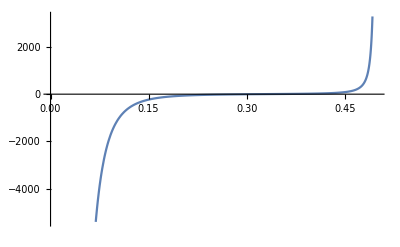

```mathematica
Plot[(-1+10 σ1^2)/(8 σ1^4 (1-4 σ1^2)^2),{σ1,0,1/2},PlotLegends->"Expressions",PlotRange->Automatic]
```

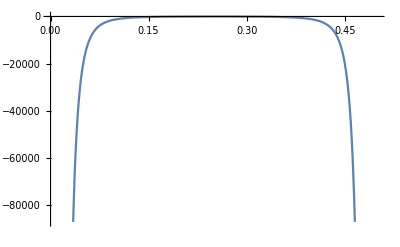

```mathematica
Plot[(1+8 σ1^2)/(4 σ1^2 (1-4 σ1^2)^2)-(1/(2!)(1/(2 P^2))^2/.{P->Min[Table[Abs[σ1-n/2],{n,-6,6}]]}),{σ1,0,1/2},PlotLegends->"Expressions",PlotRange->Automatic]
```

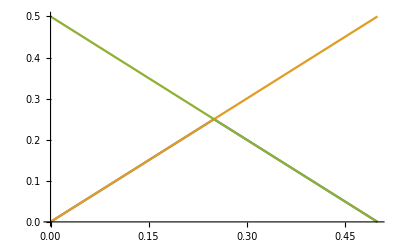

```mathematica
Plot[{Min[Table[Abs[σ1-n/2],{n,-6,6}]],σ1,1/2-σ1},{σ1,0,1/2}]
```

```mathematica
Flatten[Table[If[(a^2+b^2+c^2==2),{a,b,c},Nothing],{a,-1,1},{b,-1,1},{c,-1,1}],2]
Flatten[Table[If[(a^2+b^2+c^2==1),{a,b,c},Nothing],{a,-1,1},{b,-1,1},{c,-1,1}],2]
Flatten[2Table[If[(a^2+b^2+c^2==1),{a,b,c},Nothing],{a,-1,1},{b,-1,1},{c,-1,1}],2]
```

{{-1,-1,0},{-1,0,-1},{-1,0,1},{-1,1,0},{0,-1,-1},{0,-1,1},{0,1,-1},{0,1,1},{1,-1,0},{1,0,-1},{1,0,1},{1,1,0}}

{{-1,0,0},{0,-1,0},{0,0,-1},{0,0,1},{0,1,0},{1,0,0}}

{{-2,0,0},{0,-2,0},{0,0,-2},{0,0,2},{0,2,0},{2,0,0}}

```mathematica
(3-5 σ1^2+8 σ1^4)/(24 (σ1-5 σ1^3+4 σ1^5)^2)/.{σ1->σ1/γ}//Factor
```

(γ^6 (3 γ^4-5 γ^2 σ1^2+8 σ1^4))/(24 (γ-2 σ1)^2 (γ-σ1)^2 σ1^2 (γ+σ1)^2 (γ+2 σ1)^2)

```mathematica
(1+8 B^2)/(4 B^2 (1-4 B^2)^2)
```

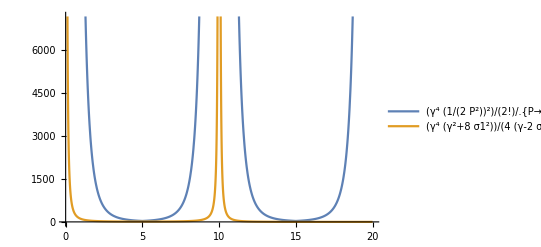

```mathematica
Plot[{γ^4 1/(2!)(1/(2 P^2))^2/.{P->Min[Table[Abs[σ1-γ n/2],{n,-6,6}]]}/.{γ->20},(γ^4 (γ^2+8 σ1^2))/(4 (γ-2 σ1)^2 σ1^2 (γ+2 σ1)^2)/.{γ->20}},{σ1,0,20},PlotLegends->"Expressions"]
```

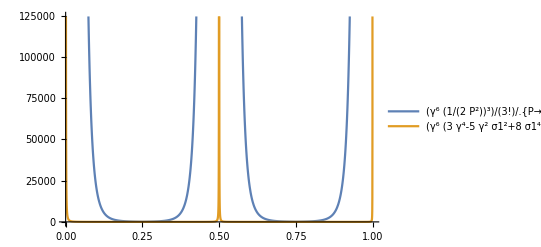

```mathematica
Plot[{γ^6 1/(3!)(1/(2 P^2))^3/.{P->Min[Table[Abs[σ1-γ n/2],{n,-6,6}]]}/.{γ->1},(γ^6 (3 γ^4-5 γ^2 σ1^2+8 σ1^4))/(24 (γ-2 σ1)^2 (γ-σ1)^2 σ1^2 (γ+σ1)^2 (γ+2 σ1)^2)/.{γ->1}},{σ1,0,1},PlotLegends->"Expressions"]
```

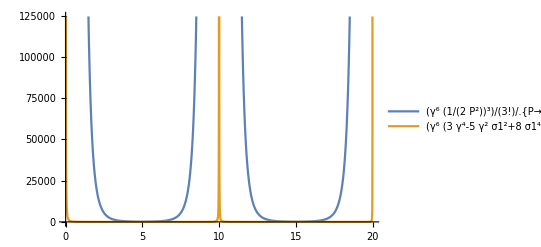

```mathematica
Plot[{γ^6 1/(3!)(1/(2 P^2))^3/.{P->Min[Table[Abs[σ1-γ n/2],{n,-6,6}]]}/.{γ->20},(γ^6 (3 γ^4-5 γ^2 σ1^2+8 σ1^4))/(24 (γ-2 σ1)^2 (γ-σ1)^2 σ1^2 (γ+σ1)^2 (γ+2 σ1)^2)/.{γ->20}},{σ1,0,20},PlotLegends->"Expressions"]
```

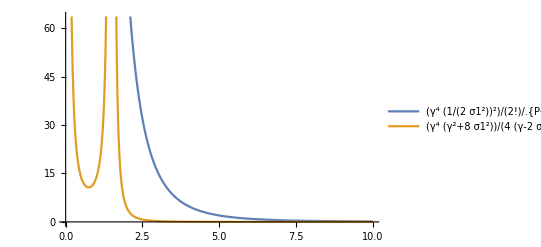

```mathematica
Plot[{γ^4 1/(2!)(1/(2 σ1^2))^2/.{P->Min[Table[Abs[σ1-n/2],{n,-6,6}]]}/.{γ->10},(γ^4 (γ^2+8 σ1^2))/(4 (γ-2 σ1)^2 σ1^2 (γ+2 σ1)^2)/.{γ->3}},{σ1,0,10},PlotLegends->"Expressions"]
```

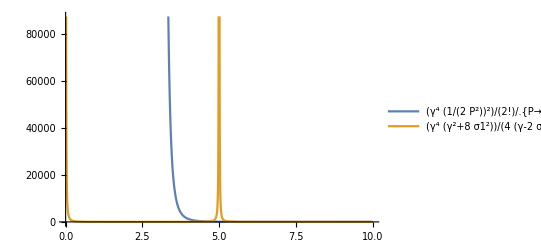

```mathematica
Plot[{γ^4 1/(2!)(1/(2 P^2))^2/.{P->Min[Table[Abs[σ1-n/2],{n,-6,6}]]}/.{γ->10},(γ^4 (γ^2+8 σ1^2))/(4 (γ-2 σ1)^2 σ1^2 (γ+2 σ1)^2)/.{γ->10}},{σ1,0,10},PlotLegends->"Expressions"]
```

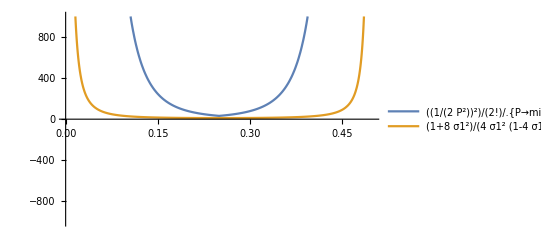

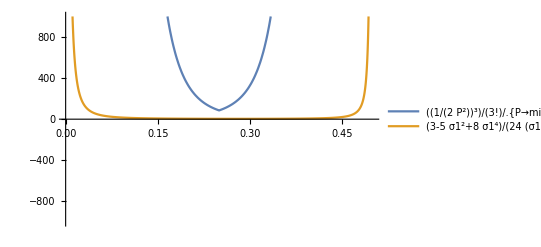

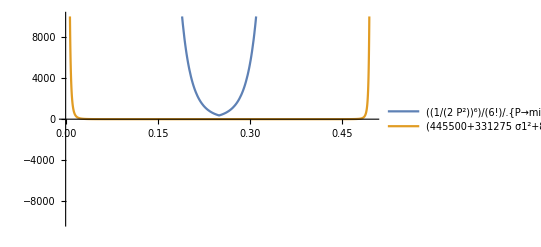

```mathematica
Plot[{1/(2!)(1/(2 P^2))^2/.{P->Min[Table[Abs[σ1-n/2],{n,-6,6}]]},(1+8 σ1^2)/(4 σ1^2 (1-4 σ1^2)^2)},{σ1,0,1/2},PlotLegends->"Expressions",PlotRange->1000]
Plot[{1/(3!)(1/(2 P^2))^3/.{P->Min[Table[Abs[σ1-n/2],{n,-10,10}]]},(3-5 σ1^2+8 σ1^4)/(24 (σ1-5 σ1^3+4 σ1^5)^2)},{σ1,0,1/2},PlotLegends->"Expressions",PlotRange->1000]
Plot[{1/(6!)(1/(2 P^2))^6/.{P->Min[Table[Abs[σ1-n/2],{n,-6,6}]]},(445500+331275 σ1^2+8565729 σ1^4-22191252 σ1^6+27425552 σ1^8-15472064 σ1^10+4409856 σ1^12-610304 σ1^14+32768 σ1^16)/(23040 σ1^4 (1-4 σ1^2)^4 (900-1669 σ1^2+969 σ1^4-216 σ1^6+16 σ1^8)^2)},{σ1,0,1/2},PlotLegends->"Expressions",PlotRange->10000]
```

```mathematica
instno=1;
tableaux=Flatten[Table[If[k1+k2+k3==instno,Table[{Y1,Y2,Y3},{Y1,IntegerPartitions[k1]},{Y2,IntegerPartitions[k2]},{Y3,IntegerPartitions[k3]}],Nothing],{k1,Range[0,instno]},{k2,Range[0,instno]},{k3,Range[0,instno]}],5];
Sum[1/(Product[ξ12[ToExpression[StringJoin["σ",ToString[i]]],ToExpression[StringJoin["σ",ToString[j]]],Y[[i]],Y[[j]]],{i,1,3},{j,1,3}])//Cancel,{Y,tableaux}]/.{e->e1+e2}/.{e->0,e1->1,e2->-1}//Together
```

-(2 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2))/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)

```mathematica
-(2 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2))/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)/.{σ3->-σ1-σ2}//Simplify
```

-(6 (σ1^2+σ1 σ2+σ2^2))/((σ1-σ2)^2 (2 σ1+σ2)^2 (σ1+2 σ2)^2)

```mathematica
1/(2!)(-(6 (σ1^2+σ1 σ2+σ2^2))/((α1)^2 (α2)^2 (α3)^2))^2/.{}
```

```mathematica
(6 (σ1^2+σ1 σ2+σ2^2))/((σ1-σ2)^2 (2 σ1+σ2)^2 (σ1+2 σ2)^2)/.{σ1->P1,σ2->P2}//Simplify
```

(6 (P1^2+P1 P2+P2^2))/((P1-P2)^2 (2 P1+P2)^2 (P1+2 P2)^2)

```mathematica
Table[σ.α/.{σ3->-σ1-σ2}/.{σ1->(α1+α2)/3,σ2->1/3 (-2 α1+α2)}//Simplify,{α,A2Roots}]
```

{-α2,-α1,α1-α2,-α1+α2,α1,α2}

```mathematica
Min[]
```

```mathematica
Solve[{σ1-σ2==α1,σ2-σ3==α3},{σ1,σ2,σ3}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{σ2→-α1+σ1,σ3→-α1-α3+σ1}}

```mathematica
Sum[(1/(Min[(({σ1,σ2,-σ1-σ2}+r).a)^2,{r,A2Lattice}]Product[If[(2 b.a)/(a.a)==1,Min[({σ1,σ2,-σ1-σ2}+r).b,{r,A2Lattice}],1],{b,A2Roots}])),{a,A2Roots}]
```

1/(Min[-3,r,(-σ1-2 σ2)^2] Min[-3,r,-2 σ1-σ2] Min[-3,r,σ1-σ2])+1/(Min[-3,r,-σ1-2 σ2] Min[-3,r,(-2 σ1-σ2)^2] Min[-3,r,-σ1+σ2])+1/(Min[-3,r,-σ1-2 σ2] Min[-3,r,(σ1-σ2)^2] Min[-3,r,2 σ1+σ2])+1/(Min[-3,r,-2 σ1-σ2] Min[-3,r,(-σ1+σ2)^2] Min[-3,r,σ1+2 σ2])+1/(Min[-3,r,σ1-σ2] Min[-3,r,(2 σ1+σ2)^2] Min[-3,r,σ1+2 σ2])+1/(Min[-3,r,-σ1+σ2] Min[-3,r,2 σ1+σ2] Min[-3,r,(σ1+2 σ2)^2])

```mathematica
Subscript[Ž, 1][1,-1,σ+r]//Simplify
```

-(2 (σ1^2+σ2^2-σ2 σ3+σ3^2-σ1 (σ2+σ3)))/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)

```mathematica
Plot3D[1/(2!)(Max[Table[Abs[Subscript[Ž, 1][1,-1,{σ1,σ2,-σ1-σ2}+r]],{r,A2Lattice}]])^2,{σ1,0,1},{σ2,σ1,1},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{1/(2!)(Max[Table[Abs[Subscript[Ž, 1][1,-1,{σ1,σ2,-σ1-σ2}+r]],{r,A2Lattice}]])^2,(9 (8 σ1^10+40 σ1^9 σ2+4 σ1^7 σ2 (-19+6 σ2^2)+σ1^8 (-19+66 σ2^2)+σ2^2 (-1+σ2^2)^2 (1-3 σ2^2+8 σ2^4)-σ1^6 (-15+σ2^2+72 σ2^4)+σ1^5 (45 σ2+263 σ2^3-132 σ2^5)+σ1^4 (-5+9 σ2^2+395 σ2^4-72 σ2^6)+σ1^3 σ2 (-10-57 σ2^2+263 σ2^4+24 σ2^6)+σ1^2 (1-15 σ2^2+9 σ2^4-σ2^6+66 σ2^8)+σ1 (σ2-10 σ2^3+45 σ2^5-76 σ2^7+40 σ2^9)))/((σ1-σ2)^2 (1+σ1-σ2)^2 (1-σ1+σ2)^2 (-1+2 σ1+σ2)^2 (2 σ1+σ2)^2 (1+2 σ1+σ2)^2 (-1+σ1+2 σ2)^2 (σ1+2 σ2)^2 (1+σ1+2 σ2)^2)},{σ1,0,1},{σ2,σ1,1},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Minimize[Table[(({σ1,σ2,-σ1-σ2}+r).{1,-1,0})^2,{r,A2Lattice}]]
```

Minimize::argbu: Minimize called with 1 argument; between 2 and 4 arguments are expected.

Minimize[{(-4+σ1-σ2)^2,(-5+σ1-σ2)^2,(-1+σ1-σ2)^2,(-2+σ1-σ2)^2,(-3+σ1-σ2)^2,(-4+σ1-σ2)^2,(-5+σ1-σ2)^2,(1+σ1-σ2)^2,(σ1-σ2)^2,(-1+σ1-σ2)^2,(-2+σ1-σ2)^2,(-3+σ1-σ2)^2,(-4+σ1-σ2)^2,(2+σ1-σ2)^2,(1+σ1-σ2)^2,(σ1-σ2)^2,(-1+σ1-σ2)^2,(-2+σ1-σ2)^2,(4+σ1-σ2)^2,(3+σ1-σ2)^2,(2+σ1-σ2)^2,(1+σ1-σ2)^2,(σ1-σ2)^2,(-1+σ1-σ2)^2,(5+σ1-σ2)^2,(4+σ1-σ2)^2,(3+σ1-σ2)^2,(2+σ1-σ2)^2,(1+σ1-σ2)^2,(5+σ1-σ2)^2,(4+σ1-σ2)^2}]

```mathematica
Plot3D[{1/(2!)((Sum[1/(Min[Table[(({σ1,σ2,-σ1-σ2}+r).a)^2,{r,A2Lattice}]]Product[If[(2 b.a)/(a.a)==1,Min[Table[({σ1,σ2,-σ1-σ2}+r).b,{r,A2Lattice}]],1],{b,A2Roots}]),{a,A2Roots}])//Simplify)^2,(9 (8 σ1^10+40 σ1^9 σ2+4 σ1^7 σ2 (-19+6 σ2^2)+σ1^8 (-19+66 σ2^2)+σ2^2 (-1+σ2^2)^2 (1-3 σ2^2+8 σ2^4)-σ1^6 (-15+σ2^2+72 σ2^4)+σ1^5 (45 σ2+263 σ2^3-132 σ2^5)+σ1^4 (-5+9 σ2^2+395 σ2^4-72 σ2^6)+σ1^3 σ2 (-10-57 σ2^2+263 σ2^4+24 σ2^6)+σ1^2 (1-15 σ2^2+9 σ2^4-σ2^6+66 σ2^8)+σ1 (σ2-10 σ2^3+45 σ2^5-76 σ2^7+40 σ2^9)))/((σ1-σ2)^2 (1+σ1-σ2)^2 (1-σ1+σ2)^2 (-1+2 σ1+σ2)^2 (2 σ1+σ2)^2 (1+2 σ1+σ2)^2 (-1+σ1+2 σ2)^2 (σ1+2 σ2)^2 (1+σ1+2 σ2)^2)},{σ1,0,1},{σ2,σ1,1},PlotLegends->Automatic]
```

```mathematica
Plot3D[{1/(2!)((6 (P1^2+P1 P2+P2^2))/((P1-P2)^2 (2 P1+P2)^2 (P1+2 P2)^2))^2/.{P1->Min[Table[Abs[σ1+n/2],{n,-3,3}]],P2->Min[Table[Abs[σ2+n/2],{n,-3,3}]]},(9 (8 σ1^10+40 σ1^9 σ2+4 σ1^7 σ2 (-19+6 σ2^2)+σ1^8 (-19+66 σ2^2)+σ2^2 (-1+σ2^2)^2 (1-3 σ2^2+8 σ2^4)-σ1^6 (-15+σ2^2+72 σ2^4)+σ1^5 (45 σ2+263 σ2^3-132 σ2^5)+σ1^4 (-5+9 σ2^2+395 σ2^4-72 σ2^6)+σ1^3 σ2 (-10-57 σ2^2+263 σ2^4+24 σ2^6)+σ1^2 (1-15 σ2^2+9 σ2^4-σ2^6+66 σ2^8)+σ1 (σ2-10 σ2^3+45 σ2^5-76 σ2^7+40 σ2^9)))/((σ1-σ2)^2 (1+σ1-σ2)^2 (1-σ1+σ2)^2 (-1+2 σ1+σ2)^2 (2 σ1+σ2)^2 (1+2 σ1+σ2)^2 (-1+σ1+2 σ2)^2 (σ1+2 σ2)^2 (1+σ1+2 σ2)^2)},{σ1,0,1},{σ2,σ1,1},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Out[1003]/.{σ2->P2,σ3->1/5}//Simplify
```

-((3796875 (13843402620479023872+17816280656952756608 σ1-27262348574295860176 σ1^2-23622581297655283328 σ1^3+24232649856262783096 σ1^4-1376665728886895160 σ1^5-8729122359745914525 σ1^6+12571050128981904000 σ1^7+429598376418892500 σ1^8-6938823798827550000 σ1^9+844805614871531250 σ1^10+1677177265365000000 σ1^11-336596614889062500 σ1^12-162278031234375000 σ1^13+43467329794921875 σ1^14))/(9802584064 (1-5 σ1)^2 (6-5 σ1)^2 (11-5 σ1)^2 (1-3 σ1)^2 (4-3 σ1)^2 (7-3 σ1)^2 (2+3 σ1)^2 (5+3 σ1)^2 (4+5 σ1)^2 (9+5 σ1)^2))

```mathematica
-(2 (σ1^2-σ1 σ2+σ2^2-σ1 σ3-σ2 σ3+σ3^2))/((σ1-σ2)^2 (σ1-σ3)^2 (σ2-σ3)^2)/.{σ1->P,σ2->1/3,σ3->1/5}//Simplify
```

-(225 (19-120 P+225 P^2))/(2 (1-8 P+15 P^2)^2)

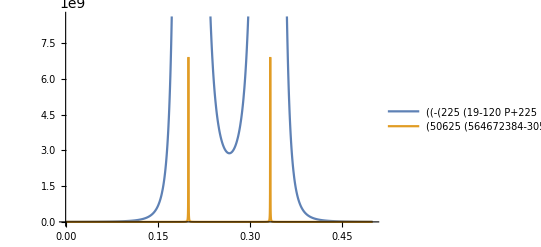

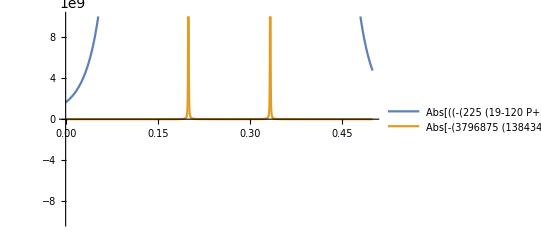

```mathematica
Plot[{1/(2!)(-(225 (19-120 P+225 P^2))/(2 (1-8 P+15 P^2)^2))^2/.{P->Min[Table[Abs[σ1-n],{n,-6,6}]]},(50625 (564672384-3058457408 σ1+2597011352 σ1^2+11386832160 σ1^3-8683138350 σ1^4-5609385000 σ1^5+7028825625 σ1^6-5661900000 σ1^7+2654015625 σ1^8))/(195364 (1-5 σ1)^2 (6-5 σ1)^2 (1-3 σ1)^2 (4-3 σ1)^2 (2+3 σ1)^2 (4+5 σ1)^2)},{σ1,0,1/2},PlotLegends->"Expressions"]
Plot[{Abs[1/(3!)(-(225 (19-120 P+225 P^2))/(2 (1-8 P+15 P^2)^2))^3]/.{P->Min[Table[Abs[σ1-n],{n,-6,6}]]},Abs[-((3796875 (13843402620479023872+17816280656952756608 σ1-27262348574295860176 σ1^2-23622581297655283328 σ1^3+24232649856262783096 σ1^4-1376665728886895160 σ1^5-8729122359745914525 σ1^6+12571050128981904000 σ1^7+429598376418892500 σ1^8-6938823798827550000 σ1^9+844805614871531250 σ1^10+1677177265365000000 σ1^11-336596614889062500 σ1^12-162278031234375000 σ1^13+43467329794921875 σ1^14))/(9802584064 (1-5 σ1)^2 (6-5 σ1)^2 (11-5 σ1)^2 (1-3 σ1)^2 (4-3 σ1)^2 (7-3 σ1)^2 (2+3 σ1)^2 (5+3 σ1)^2 (4+5 σ1)^2 (9+5 σ1)^2))]},{σ1,0,1/2},PlotLegends->"Expressions",PlotRange->10^10]
```